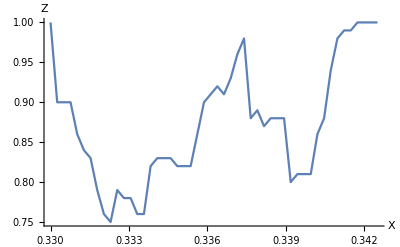

```mathematica
X =Transpose[Import["/home/koritskiy/rqc/ferrimagnet/confusion_learning/results/2d/X.dat"]][[1]];
Zcut =Flatten[Import["/home/koritskiy/rqc/ferrimagnet/confusion_learning/results/2d/Z_cut.dat"]];
Final =Table[{X[[i]], Zcut[[i]]}, {i, 1, Length[X]}];
ListLinePlot[Final, AxesLabel->{"X", "Z"}]
```

```mathematica
Integrate [1/(x(1+x^2)), x]
```

Log[x]-1/2 Log[1+x^2]